```mathematica
a = 0.5
```

0.5

```mathematica
{"e1",Slider[Dynamic[e1],{-0.1,0.1,0.01}],Dynamic[e1]}
{"e2",Slider[Dynamic[e2],{-0.1,0.1,0.01}],Dynamic[e2]}
{"e3",Slider[Dynamic[e3],{-0.1,0.1,0.01}],Dynamic[e3]}
```

{e1,,}

{e2,,}

{e3,,}

```mathematica
sol =Quiet@NDSolve[{x''[t] == -(2*a*x[t] +3*e1*(x[t])^2 +3*e3*(x[t])^2*(y[t])^3),x[0]==0,x'[0]==1,y''[t] == -(2*a*y[t] +3*e2*(y[t])^2 +3*e3*(x[t])^3*(y[t])^2),y[0]==1,y'[0]==0},{x[t],y[t]},{t,0,200}]
```

{{x[t]→InterpolatingFunction[{{0., 200.}}, <>][t],y[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

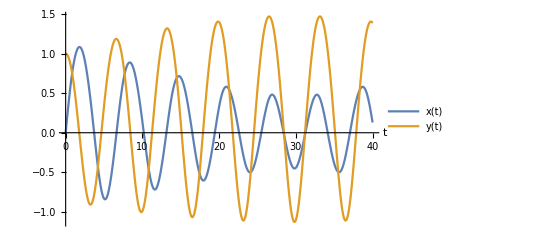

```mathematica
output1 = Plot[{x[t]/.sol, y[t]/.sol}, {t,0,40}, PlotLegends->{"x(t)","y(t)"},AxesLabel->Automatic]
```

```mathematica
dat=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol,{t,0,tt},PlotRange->2,AxesLabel->{x[t],y[t]}]],{tt,.1,200,.2}];
```

```mathematica
ListAnimate[dat]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["visual_case9.gif",dat]
```

/home/jack/Documents/Wolfram Mathematica

visual_case9.gif

```mathematica
Export["solution_case9.svg",output1]
```

solution_case9.svg